```mathematica
g=9.8(*grav. constant*)
(*vter = Sqrt[m g/c]*)
V = 50
th = 50*Pi/180
sol = With[{vter=100}, NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]]
```

9.8

50

(5 π)/18

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

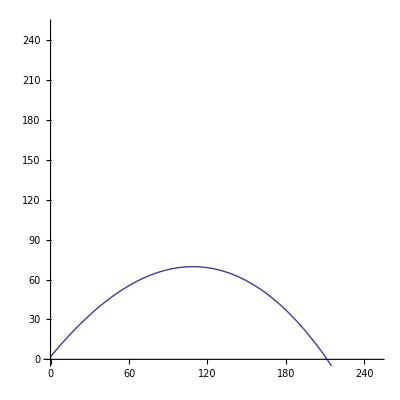

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200}, PlotRange-> {0,250}]
```

```mathematica
Manipulate[
Module[
{[sol=NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]),{y[0]==2,x[0]==0},{y'[0]==V Sin[th],x'[0]==V Cos[th]}},{x,y},{t,0,200}]]},
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotRange->{0,250}]],
{{V,0.5,"Initial Velocity (m/s)"},0,100,Appearance->"Labeled"},{{th,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{vter,0,"Terminal Velocity (rad/s)"},0,100.,Appearance->"Labeled"},
{{t,0,"Time (s))"},0,20.,Appearance->"Labeled"}]
```